```mathematica
Pi
```

π

```mathematica
N[%, 10]
```

3.141592654

```mathematica
chud[n_]:=N[1/(12*Sum[((-1)^k*(6 k)!*(13591409+545140134 k))/((3 k)!*(k!)^3*640320^(3 k+3/2)),{k,0,n}]),5];
```

```mathematica
chud[1]
```

3.1416

```mathematica
chud[2]
```

3.1416

```mathematica
mc[n_]:=Module[{in=0,total=0},For[k=1,k≤n,k=k+1,x=RandomReal[];
y=RandomReal[];
total=total+1;
If[x*x+y*y≤1,in=in+1]];
N[in/total*4,5]];
```

```mathematica
Print[mc[1000000]];
```

3.1431

```mathematica
primep[n_]:=Module[{machineid=61029079751506,(*maximum range of random number.*)is=0,total=0},For[k=1,k≤n,k=k+1,total=total+1;
x=RandomInteger[{1,machineid}];
y=RandomInteger[{1,machineid}];
If[GCD[x,y]==1,is=is+1]];
If[is==0,0,N[Sqrt[6/(is/total)],5]]];
```

```mathematica
For[i=1,i≤5,i=i+1,Print[primep[10000]]];
```

3.1591

3.1463

3.1448

3.1383

3.1578

{3.1416,3.1416,3.1416,3.1416,3.1416}

{3.1416,3.1416,3.1416,3.1416,3.1416}

{2.6667,2.2857,2.9474,3.0189,3.084}

{4.2426,2.8983,2.8536,3.5665,3.0589}

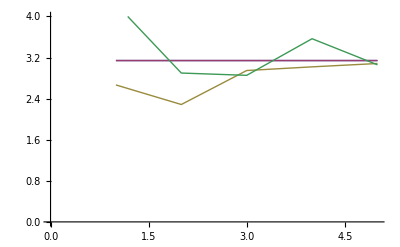

```mathematica
n=5;
pis=Table[N[Pi,5],{k,1,n}];
chuds=Table[chud[k],{k,1,n}];
mcs=Table[mc[Prime[2^k]],{k,1,n}];
primeps=Table[primep[Prime[2^k]],{k,1,n}];
Print[pis];
Print[chuds];
Print[mcs];
Print[primeps];
ListLinePlot[{pis,chuds,mcs,primeps},AxesOrigin->{0,0},PlotRange->{0,4}]
```

{3.1416,3.1416,3.1416,3.1416,3.1416,3.1416,3.1416,3.1416,3.1416,3.1416}

{3.1416,3.1416,3.1416,3.1416,3.1416,3.1416,3.1416,3.1416,3.1416,3.1416}

{2.6667,2.2857,3.7895,3.1698,3.1145,3.1511,3.0765,3.076,3.1871,3.0942}

{3.,3.2404,2.9613,3.3114,3.3509,3.1421,3.0928,3.15,3.1372,3.149}

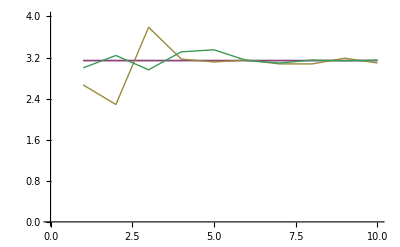

```mathematica
n=10;
pis=Table[N[Pi,5],{k,1,n}];
chuds=Table[chud[k],{k,1,n}];
mcs=Table[mc[Prime[2^k]],{k,1,n}];
primeps=Table[primep[Prime[2^k]],{k,1,n}];
Print[pis];
Print[chuds];
Print[mcs];
Print[primeps];
ListLinePlot[{pis,chuds,mcs,primeps},AxesOrigin->{0,0},PlotRange->{0,4}]
```